#### The network

```mathematica
(*
BernoulliGraphDistribution[n,ped];
n = number of nodes;
ped = edges probability;
*)

n=500; ped=0.05;
net=RandomGraph[BernoulliGraphDistribution[n,ped],VertexLabels->""];
maxcomp=Max[Length[#]&/@ConnectedComponents[net]];

{net,maxcomp};
```

#### Infected neighbors

```mathematica
(*This function returns the number and the list of infected neighbors of a given node*)

infneighs[ntwk_,nodeid_,neighsize_,ilist_]:=
Module[{ntw=ntwk,node=nodeid, ns=neighsize},

inf=Flatten@Position[ilist,1];

neighlist=IncidenceList[ntw,node,ns][[;;,2]];(*Delete[VertexList@NeighborhoodGraph[ntw,node,ns],1];*)

Do[
 ids=MemberQ[inf,#]&/@neighlist;

pos=Flatten[Position[ids,True]];

infneigh=neighlist[[#]]&/@ pos;

,{r,1,Length[neighlist]}
];

Return[{node,Length[infneigh],infneigh}]
]
```

#### Node maximizer

```mathematica
(*Single peak function*)
fs[x_,y_,z_]:=(x z -z^2)^y

(* The maxer code runs the optimization process for each vertex *)
vertxmaxer[ntwk_,nodeid_,dispars_,u_,neis_]:=
Module[{
ntw=ntwk, (* network used *)
node=nodeid[[1]], maxed=nodeid[[2]], (* the node for which the maximizer is running and the information about inf neghbours *)
β=dispars[[1]],γ=dispars[[2]], (*disease parameters*)
T=u ,(*time horizon*)
ns=neis (* Neighboorhood size to get the local prevalence*)
},

(*maxer[u_,v_,w_]:=*)
ν=0.05;

b=2*maxed; (* maximum possible # of edges for the utility function, the optimal utility is assumed at half of this*)
δ=0.99986; (*discount factor*)

(* Vector storing the optimal s utility *)
EUS=Table[0,{t,1,T+1}];

(* The last step in s assumes to use all edges *)
EUS[[-1]]=fs[b,ν,maxed];

(* Vector storaging the optimal i utility *)
EUI=Table[0,{t,1,T+1}];

(* Vector storaging the optimal i utility *)
EUR=Table[0,{t,1,T+1}];

(* The last step in r assumes to use all edges *)
(*EUR[[-1]]=fs[b,ν,maxed];*)

(* Vector storing the optimal # of edges for the susceptible node during the planning horizon *)
nedgest=Table[0,{i,1,T+1}];

nedgest[[-1]]=maxed;

(*Pt is the probability of disease transmission along an edge during a single time step*)
Pt=β; Pir=γ;

(* Optimization procedure *)
For[t=T,t≥ 1,t--, (* Horizon times, this goes backwards *)

(* individual's utility starts at zero*)
maxu=0;

(*(* Reset the list of neighbors, to start the new optimization *)
newnodeneighs=nodeneighs;*)

(* Evaluating all the contact rates for susceptible individuals, all possible variable states *)
Do[

Psi=1-(1-Pt)^edgesd;

(* Evaluating the expected utilities *)

(*Utility gained by being currently susceptible*)
EUS[[t]]= fs[b,ν,edgesd] +δ((1-Psi) EUS[[t+1]]+Psi EUI[[t+1]]);

EUI[[t]]=(0)fs[b,ν,maxed]+ δ( (1-Pir) EUI[[t+1]]+Pir EUR[[t+1]] );

EUR[[t]]=fs[b,ν,maxed]+δ EUR[[t+1]];

(*Compare the new utility with the previous one, if it's bigger, then adapt the behavior *)
If[EUS[[t]]>maxu,nedgest[[t]]=edgesd;maxu=EUS[[t]]];

,{edgesd,maxed,1,-1}]
];
Clear[t];
Return[nedgest]
]
```

### Multiple epidemics

#### Mean over multiple epidemics - no behavior

```mathematica
epis=200;

epidist=ParallelTable[

(*(*Create the network*)
n=500; ped=0.05;
net=RandomGraph[BernoulliGraphDistribution[n,ped],VertexLabels->""];*)

(*Define iterations #*)
it=100;

(*Declare infected, susceptible and recovered vectors*)
Clear[i,s];
i0=RandomInteger[n];
i=Table[If[k==i0,1,0],{k,1,n}];
s=Table[1,{k,1,n}]-i;
r=Table[0,{k,1,n}];

pi=(*0.05*)0.05; (*Infection prob.*)
pr=0.04; (*Recovery prob.*)

epi=Table[

(* # of infected neighboors per node *)
infn=AdjacencyMatrix[net].i; 
ninfp=1-(1-pi)^#&/@infn;

(*Newly infected nodes*)
x=RandomReal[1,n];
newinf=Boole[Thread[x≤ninfp]];
upi=Table[If[s[[k]]==1&&newinf[[k]]==1,1,0],{k,1,n}];

(*Update S and I vectors: after infections*)
inew=i+upi;
snew=s-upi;

y=RandomReal[1,n];
newrec=Boole[Thread[y≤pr]];

(*Update I and R vectors: after recovery*)
upr=Table[If[inew[[k]]==1&&newrec[[k]]==1,1,0],{k,1,n}];

rnew=r+upr;
inew=inew-upr;
 
(*Update variable vectors*)
s=snew; i=inew;r=rnew;

{Count[snew,1],Count[inew,1],Count[rnew,1]}

,{l,2,it}];

epi

,{k,1,epis}];

(*ListLinePlot[epi[[;;,2]]/n,PlotRange->{0,1}]*)
```

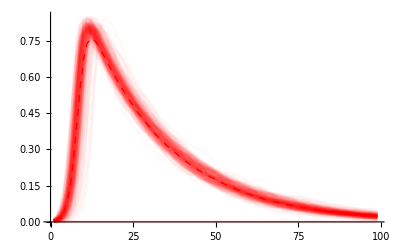

```mathematica
allplots=ListLinePlot[epidist[[;;,;;,2]]/n,PlotStyle->Directive[{Red,Opacity[0.025]}]];
meanplot=ListLinePlot[Mean@epidist[[;;,;;,2]]/n,PlotStyle->{Dashed,Red,Thick}];
plotnob=Show[allplots,meanplot]
```

#### Mean over multiple epidemics - behavior

```mathematica
bepis=200; (*Iterations of epidemics*)
ns=1; (*Neighborhood size*)

bepidist=ParallelTable[

(*(*Create the network*)
n=500; ped=0.05;
net=RandomGraph[BernoulliGraphDistribution[n,ped],VertexLabels->""];
*)
(*Define iterations #*)
it=100;

(*Declare infected, susceptible and recovered vectors*)
Clear[i,s];
i0=RandomInteger[n];
i=Table[If[k==i0,1,0],{k,1,n}];
s=Table[1,{k,1,n}]-i;
r=Table[0,{k,1,n}];

pi=(*0.05*)0.05; (*Infection prob.*)
pr=0.04; (*Recovery prob.*)

T=7; (*Planning horizon*)
ns=1; (*Neighborhood size*)

rednet=net;

epib=Table[

(* # of infected neighboors per node *)
infn=AdjacencyMatrix[rednet].i; 
ninfp=1-(1-pi)^#&/@infn;

(*Newly infected nodes*)
x=RandomReal[1,n];
newinf=Boole[Thread[x≤ninfp]];
upi=Table[If[s[[k]]==1&&newinf[[k]]==1,1,0],{k,1,n}];

(*Update S and I vectors: after infections*)
inew=i+upi;
snew=s-upi;

y=RandomReal[1,n];
newrec=Boole[Thread[y≤pr]];

(*Update I and R vectors: after recovery*)
upr=Table[If[inew[[k]]==1&&newrec[[k]]==1,1,0],{k,1,n}];

rnew=r+upr;
inew=inew-upr;
 
(*Update variable vectors*)
s=snew; i=inew;r=rnew;


(* =-=-= The maximization process =-=-= *)

rednet=net; (*Define a dummy network: this is the network to play with*)

(*Get the info of all susceptible nodes at time t*)
sus=Flatten@Position[s,1];
infofsus=infneighs[net,#,ns,i]&/@sus;

(*Get only the info of susceptible with  infected neighbours*)
susinfs=Table[If[infofsus[[k,2]]≠0,infofsus[[k]]],{k,1,Length@sus}]/.Null->Sequence[];

(* Use the maximizer to define how many edges to drop: it returns the number of edges to leave *)
redneighs=Table[vertxmaxer[net,susinfs[[k]],{pi,pr},T,ns][[1]],{k,1,Length[susinfs]}];

(*Get the list of the form {susceptible  id,{list of infected neighbours to remove}}*)
list=Table[{susinfs[[k,1]],RandomSample[susinfs[[k,3]],susinfs[[k,2]]-redneighs[[k]]]},{k,1,Length[redneighs]}];

(*Create the list of all the edges to remove at time t: of the form {s,i-rem}*)
edgestorem=Flatten[
Table[
{list[[k,1]]<->#}&/@list[[k,2]]
,{k,1,Length@redneighs}]];

(*Drop edges from the network*)
rednet=EdgeDelete[rednet,edgestorem];

{Count[s,1],Count[i,1],Count[r,1],EdgeCount[rednet],
N@Mean[Length[IncidenceList[rednet,#]]&/@sus]}

,{l,2,it}];

epib

,{z,1,bepis}];
```

#### Define the plots

```mathematica
(*Infected population dynamics - classic model*)
tseries=epidist[[;;,;;,2]]/n;

(*Infected population dynamics - classic model*)
tseriesrec=epidist[[;;,;;,3]]/n;

(*Total number of edges in the network*)
edglist=bepidist[[;;,;;,4]]/EdgeCount[net];

(*Infected population dynamics - adaptive model*)
btseriesinf=bepidist[[;;,;;,2]]/n;

(*Susceptible population dynamics - adaptive model*)
btseriessus=bepidist[[;;,;;,1]]/n;

(*Recovered population dynamics - adaptive model*)
btseriesrec=bepidist[[;;,;;,3]]/n;

(*Susceptible inds. mean number of edges*)
susedglist=bepidist[[;;,;;,5]]/N@Mean@VertexDegree[net];
```

#### Static network vs adaptive network dynamics

Infected individuals dynamics

C:/Users/jimmy/OneDrive/Desktop/Master_Applied_Math/Tesis/adaptive_networks/dis_prev_comp.pdf

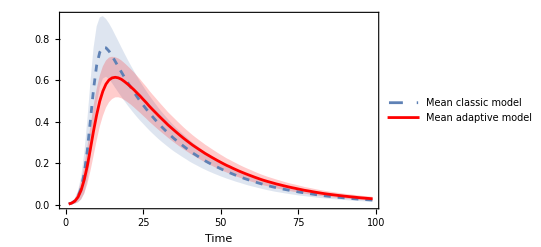

```mathematica
(*Static network disease dynamics*)
complot=ListLinePlot[
{Mean@tseries,
Mean@tseries+StandardDeviation[N@tseries],
Mean@tseries-StandardDeviation[N@tseries],
Mean@btseriesinf,
Mean@btseriesinf+StandardDeviation[N@btseriesinf],
Mean@btseriesinf-StandardDeviation[N@btseriesinf]
},
Filling->{{1->{3}},1->{2},{4->{6}},4->{5}},
PlotStyle->{Directive[Thick,Dashed],None,None, Directive[Thick,Red],None,None},
TicksStyle->Directive[Bold, 14],
PlotRange->{All,All},
BaseStyle->{FontFamily->"Cambria Math",12},
LabelStyle->{FontFamily->"Cambria Math", 12},
(*PlotLabel->Style["Disease Prevalence", FontSize->14, FontColor->Black],*)
Frame -> True,
FrameLabel->{Style["Time", Black, Bold], None},
PlotLegends->Placed[{"Mean classic model", None, None,"Mean adaptive model", None, None}, Below]
];
Export["C:/Users/jimmy/OneDrive/Desktop/Master_Applied_Math/Tesis/adaptive_networks/dis_prev_comp.pdf",complot,"PDF","AllowRasterization"->False]
complot
```

```mathematica
Export["C:/Users/jimmy/OneDrive/Desktop/Master_Applied_Math/Tesis/adaptive_networks/plot1.pdf",p,"PDF","AllowRasterization"->False]
```

C:/Users/jimmy/OneDrive/Desktop/Master_Applied_Math/Tesis/adaptive_networks/plot1.pdf

```mathematica
SystemOpen["C:/Users/jimmy/OneDrive/Desktop/Master_Applied_Math/Tesis/adaptive_networks/plot1.pdf"]
```

Recovered individuals dynamics

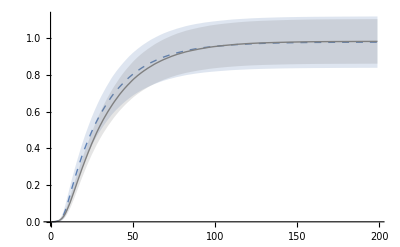

```mathematica
pconst=ListLinePlot[{Mean@tseriesrec,Mean@tseriesrec+StandardDeviation[N@tseriesrec],Mean@tseriesrec-StandardDeviation[N@tseriesrec]},Filling->{{1->{3}},1->{2}},PlotRange->All,PlotStyle->{Directive[Thick,Dashed],None,None},TicksStyle->Directive[Bold, 14]];

pbehavrec=ListLinePlot[{Mean@btseriesrec+StandardDeviation[N@btseriesrec],Mean@btseriesrec,Mean@btseriesrec-StandardDeviation[N@btseriesrec]},Filling->{{2->{3}},2->{1}},PlotRange->All,PlotStyle->{None,Directive[Thick,Gray],None},TicksStyle->Directive[Bold, 14]];

Show[pconst,pbehavrec]
```

#### Behavioral response: population vs individual scale

C:/Users/jimmy/OneDrive/Desktop/Master_Applied_Math/Tesis/adaptive_networks/global_local_resp.pdf

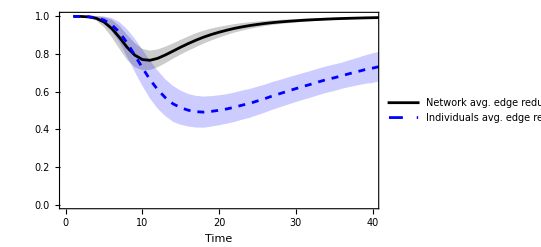

```mathematica
(*Total population activity dynamics*)
redplot=ListLinePlot[
{Mean@edglist,
Mean@edglist+StandardDeviation[N@edglist],
Mean@edglist-StandardDeviation[N@edglist],
Mean@susedglist,
Mean@susedglist+StandardDeviation[N@susedglist],
Mean@susedglist-StandardDeviation[N@susedglist]
},
Filling->{{1->{3}},1->{2},{4->{6}},4->{5}},
PlotStyle->{Directive[Thick,Black],None,None, Directive[Thick,Dashed,Blue],None,None},
TicksStyle->Directive[Bold, 14],
PlotRange->{{0,40},All},
BaseStyle->{FontFamily->"Cambria Math",12},
LabelStyle->{FontFamily->"Cambria Math", 12},
(*PlotLabel->Style["Global and local behavioral responses", FontSize->14, FontColor->Black],*)
Frame -> True,
FrameLabel->{Style["Time", Black, Bold], None},
PlotLegends->Placed[{"Network avg. edge reduction", None, None,"Individuals avg. edge reduction", None, None}, Below]
];
Export["C:/Users/jimmy/OneDrive/Desktop/Master_Applied_Math/Tesis/adaptive_networks/global_local_resp.pdf",redplot,"PDF","AllowRasterization"->False]
redplot
```

C:/Users/jimmy/OneDrive/Desktop/Master_Applied_Math/Tesis/adaptive_networks/global_resp.pdf

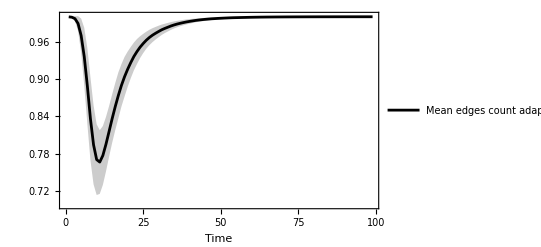

```mathematica
(*Static network disease dynamics*)
popplot=ListLinePlot[
{Mean@edglist,
Mean@edglist+StandardDeviation[N@edglist],
Mean@edglist-StandardDeviation[N@edglist]
},
Filling->{{1->{3}},1->{2}},
PlotStyle->{Directive[Thick,Black],None,None},
TicksStyle->Directive[Bold, 14],
PlotRange->{All,All},
BaseStyle->{FontFamily->"Cambria Math",12},
LabelStyle->{FontFamily->"Cambria Math", 12},
(*PlotLabel->Style["B) Network Structure", FontSize->14, FontColor->Black],*)
Frame -> True,
FrameLabel->{Style["Time", Black, Bold], None},
PlotLegends->Placed[{"Mean edges count adaptive model", None, None}, Below]
];
Export["C:/Users/jimmy/OneDrive/Desktop/Master_Applied_Math/Tesis/adaptive_networks/global_resp.pdf",popplot,"PDF","AllowRasterization"->False]
popplot
```

#### Individual adaptive response and susceptible nodes

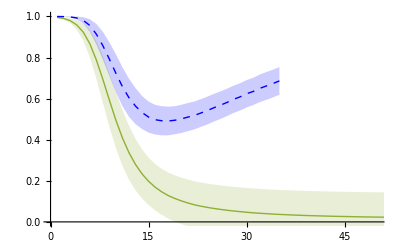

```mathematica
pbehavsus=ListLinePlot[{Mean@btseriessus+StandardDeviation[N@btseriessus],Mean@btseriessus-StandardDeviation[N@btseriessus],Mean@btseriessus},Filling->{{3->{2}},3->{1}},PlotRange->All,PlotStyle->{None,None,Thick},TicksStyle->Directive[Bold, 14]];

Show[pbehavsus,susredplot,PlotRange->{{0,50},{0,1}}]
```

C:/Users/jimmy/OneDrive/Desktop/Master_Applied_Math/Tesis/adaptive_networks/pop_dyn_local_resp.pdf

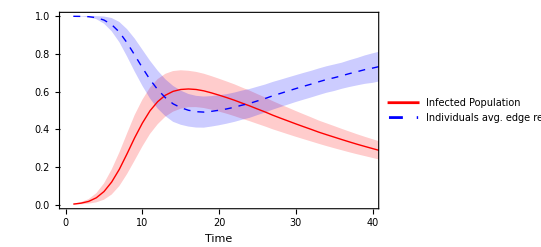

```mathematica
complot2=ListLinePlot[
{Mean@btseriesinf,
Mean@btseriesinf+StandardDeviation[N@btseriesinf],
Mean@btseriesinf-StandardDeviation[N@btseriesinf],
Mean@susedglist,
Mean@susedglist+StandardDeviation[N@susedglist],
Mean@susedglist-StandardDeviation[N@susedglist]
},
Filling->{{1->{3}},1->{2},{4->{6}},4->{5}},
PlotStyle->{Directive[Thick,Red],None,None, Directive[Thick,Dashed,Blue],None,None},
TicksStyle->Directive[Bold, 14],
PlotRange->{{0,40},All},
BaseStyle->{FontFamily->"Cambria Math",12},
LabelStyle->{FontFamily->"Cambria Math", 12},
(*PlotLabel->Style["B) Population Dynamics and local behavioral response", FontSize->14, FontColor->Black],*)
Frame -> True,
FrameLabel->{Style["Time", Black, Bold], None},
PlotLegends->Placed[{"Infected Population", None, None,"Individuals avg. edge reduction", None, None}, Below]
];
Export["C:/Users/jimmy/OneDrive/Desktop/Master_Applied_Math/Tesis/adaptive_networks/pop_dyn_local_resp.pdf",complot2,"PDF","AllowRasterization"->False]
complot2
```

C:/Users/jimmy/OneDrive/Desktop/Master_Applied_Math/Tesis/adaptive_networks/global_local_resp_dist.pdf

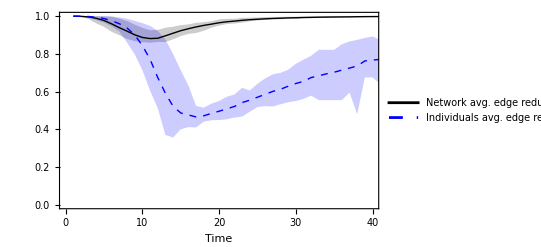

```mathematica
(*Total population activity dynamics*)

meanEdgelist = {0.99977,0.99882,0.99589,0.98836,0.97689,0.95892,0.93877,0.92044,0.90122,0.887,0.88117,0.88277,0.89581,0.90944,0.92282,0.93331,0.94271,0.95098,0.95759,0.96488,0.97015,0.97359,0.97793,0.98106,0.98347,0.9856,0.98767,0.98896,0.9905,0.9914,0.99266,0.99349,0.99437,0.99494,0.99544,0.99582,0.99619,0.99691,0.99732,0.99753,0.99778,0.99799,0.9983,0.9985,0.99859,0.99874,0.99891,0.99902,0.99909,0.99915,0.99923,0.99927,0.99932,0.99936,0.9994,0.99946,0.9996,0.99964,0.99969,0.99974,0.99976,0.9998,0.99983,0.99984,0.99984,0.99984,0.99986,0.99986,0.99986,0.99986,0.99987,0.99989,0.99991,0.99991,0.99993,0.99994,0.99994,0.99994,0.99995,0.99998,0.99998,0.99998,0.99999,0.99999,0.99999,0.99999,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0};

minEdgeList = {1.0,1.0,1.0,0.99936,0.99872,0.9968,0.98672,0.97375,0.95535,0.93838,0.92526,0.92686,0.93838,0.94366,0.95246,0.95615,0.96463,0.96815,0.97295,0.98271,0.98576,0.98608,0.99088,0.99216,0.99264,0.9952,0.99568,0.99616,0.9968,0.99728,0.99744,0.9976,0.9984,0.99856,0.99856,0.99856,0.99856,0.99872,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0};

maxEdgeList = {0.99872,0.99504,0.9848,0.96143,0.94334,0.91677,0.89885,0.879,0.86732,0.8622,0.85883,0.86284,0.86284,0.87724,0.89421,0.90589,0.91069,0.92222,0.93838,0.94958,0.95791,0.96063,0.96543,0.97247,0.97711,0.98031,0.98239,0.98287,0.98544,0.98624,0.98896,0.98944,0.98976,0.9904,0.99168,0.99184,0.99344,0.99424,0.99456,0.99536,0.99552,0.99568,0.996,0.99648,0.9968,0.99696,0.99712,0.99712,0.99744,0.99776,0.99776,0.99792,0.99808,0.99824,0.9984,0.9984,0.9984,0.99872,0.99888,0.99888,0.99888,0.99888,0.99888,0.99904,0.99904,0.99904,0.99904,0.99904,0.99904,0.99904,0.99904,0.9992,0.99936,0.99936,0.99936,0.99936,0.99936,0.99936,0.99936,0.99984,0.99984,0.99984,0.99984,0.99984,0.99984,0.99984,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0};

meanEdgeListSusc = {0.99989,0.99942,0.99793,0.99387,0.98718,0.97562,0.9596,0.93721,0.90047,0.84417,0.77156,0.67503,0.59141,0.52252,0.48715,0.47663,0.46602,0.47197,0.48512,0.4963,0.50878,0.52158,0.54224,0.55475,0.5706,0.58567,0.60134,0.61267,0.62873,0.6432,0.65435,0.67463,0.68395,0.69449,0.70289,0.71424,0.72488,0.73608,0.76266,0.76721,0.77094,0.78191,0.7916,0.7948,0.80559,0.81741,0.83341,0.84788,0.84807,0.85712,0.86871,0.87605,0.88204,0.88683,0.89474,0.90368,0.92205,0.92937,0.93211,0.94235,0.9502,0.95542,0.96187,0.95976,0.95976,0.95976,0.96072,0.96072,0.95701,0.95574,0.95532,0.95983,0.96533,0.96533,0.97349,0.97518,0.97518,0.97518,0.98444,0.9879,0.99295,0.99295,0.99728,0.99728,0.99728,0.99728,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0};

minEdgeListSusc = {1.0,1.0,1.0,0.99972,0.99943,0.99845,0.99307,0.9858,0.97482,0.96277,0.94847,0.9223,0.87561,0.80004,0.71341,0.63238,0.52448,0.51509,0.5364,0.55074,0.57286,0.58506,0.62032,0.60614,0.64129,0.67,0.69167,0.69967,0.716,0.74754,0.76934,0.79008,0.82157,0.82157,0.82157,0.85114,0.86595,0.8741,0.88452,0.89259,0.87444,0.90278,0.90278,0.90278,0.90278,0.9213,0.9213,0.92593,0.92,0.93722,0.93722,0.93722,0.94667,0.94667,0.98,0.98,0.98,0.98,0.98,0.98,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0};

maxEdgeListSusc = {0.9994,0.99766,0.99243,0.97861,0.96604,0.94491,0.91803,0.86039,0.79813,0.71397,0.60559,0.51312,0.37078,0.35706,0.40071,0.41208,0.41026,0.44092,0.44885,0.44935,0.45362,0.46256,0.46813,0.49364,0.51851,0.52335,0.52107,0.53296,0.54394,0.55032,0.56175,0.57888,0.555,0.555,0.555,0.555,0.595,0.48,0.67545,0.67545,0.6404,0.59091,0.59091,0.59091,0.59091,0.59091,0.72727,0.76721,0.76721,0.78261,0.78804,0.78804,0.80888,0.80888,0.80888,0.80888,0.79167,0.79167,0.79167,0.83333,0.875,0.90807,0.90807,0.91667,0.91667,0.91667,0.91667,0.91667,0.875,0.875,0.875,0.875,0.875,0.875,0.91667,0.91667,0.91667,0.91667,0.94705,0.95455,0.95833,0.95833,0.97826,0.97826,0.97826,0.97826,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0};


redplot=ListLinePlot[
{meanEdgelist,
minEdgeList ,
maxEdgeList ,
meanEdgeListSusc,
minEdgeListSusc,
maxEdgeListSusc 
},
Filling->{{1->{3}},1->{2},{4->{6}},4->{5}},
PlotStyle->{Directive[Thick,Black],None,None, Directive[Thick,Dashed,Blue],None,None},
TicksStyle->Directive[Bold, 14],
PlotRange->{{0,40},All},
BaseStyle->{FontFamily->"Cambria Math",12},
LabelStyle->{FontFamily->"Cambria Math", 12},
(*PlotLabel->Style["Global and local behavioral responses", FontSize->14, FontColor->Black],*)
Frame -> True,
FrameLabel->{Style["Time", Black, Bold], None},
PlotLegends->Placed[{"Network avg. edge reduction", None, None,"Individuals avg. edge reduction", None, None}, Below]
];
Export["C:/Users/jimmy/OneDrive/Desktop/Master_Applied_Math/Tesis/adaptive_networks/global_local_resp_dist.pdf",redplot,"PDF","AllowRasterization"->False]
redplot
```